```mathematica
SetDirectory[NotebookDirectory[]];
```

## Collinear

### ϕ integral

```mathematica
Assuming[0<ϵ<1/2,FullSimplify[Integrate[Sin[ϕ]^(-2ϵ),{ϕ,0,Pi}]]]
```

(√π Gamma[1/2-ϵ])/Gamma[1-ϵ]

### z integral

```mathematica
Series[1/z^ϵ 1/(1-z)^ϵ((1+(1-z)^2)/z-ϵ z),{ϵ,0,1}]
```

(2-2 z+z^2)/z+(-z+((2-2 z+z^2) (-Log[1-z]-Log[z]))/z) ϵ+O[ϵ]^2

```mathematica
Assuming[0<c<1/2,Integrate[(2-2z+z^2)/z ,{z,c,1-c}]]
```

-3/2+3 c+2 Log[-1+1/c]

```mathematica
FullSimplify[Assuming[0<c<1/2,Integrate[z+((2-2 z+z^2) (Log[1-z]+Log[z]))/z,{z,c,1-c}]]]/.c->zcut
```

7/2-7 zcut+Log[1-zcut] (-3+3 zcut+Log[1-zcut])+3 zcut Log[zcut]-Log[zcut]^2-2 PolyLog[2,1-zcut]+2 PolyLog[2,zcut]

### series expansion

```mathematica
FullSimplify[Series[2/Gamma[1-ϵ]((4μ^2)/Q^2)^ϵ,{ϵ,0,1}]]
```

2+(-2 EulerGamma+Log[16]+2 Log[μ^2/Q^2]) ϵ+O[ϵ]^2

### bounds

```mathematica
Reduce[1-ρ/4<1-zcut,ρ]
```

zcut∈ℝ&&ρ>4 zcut

## Soft and collinear

```mathematica
Assuming[{0<ϵ<1,0<zcut<1/2},Integrate[1/z^(1+ϵ),{z,zcut,Infinity}]]
```

zcut^-ϵ/ϵ

```mathematica
Series[zcut^-ϵ/ϵ,{ϵ,0,1}]
```

1/ϵ-Log[zcut]+1/2 Log[zcut]^2 ϵ+O[ϵ]^2

```mathematica
FullSimplify[Series[1/Gamma[1-ϵ]((4 μ^2)/Q^2)^ϵ zcut^-ϵ/ϵ,{ϵ,0,1}]/.EulerGamma->0]
```

1/ϵ+(-Log[zcut]+Log[(4 μ^2)/Q^2])+1/12 (-π^2+6 Log[4]^2-12 Log[4] Log[zcut]+6 Log[zcut]^2+6 Log[μ^2/Q^2] (-2 Log[zcut]+Log[(16 μ^2)/Q^2])) ϵ+O[ϵ]^2

## Combined

```mathematica
Assuming[{μ>0,Q>0,0<ρ<1},FullSimplify[Series[(Q μ^(2ϵ))/(2Gamma[1-ϵ])(4/Q)^(1+2ϵ)1/ϵ 1/ρ^ϵ,{ϵ,0,1}]]/.EulerGamma->0]
```

2/ϵ-2 Log[(Q^2 ρ)/(16 μ^2)]+(-π^2/6+16 Log[2]^2+(2 (Log[Q]-Log[16 μ])+Log[ρ]) Log[(Q^2 ρ)/μ^2]) ϵ+O[ϵ]^2

```mathematica
Assuming[{μ>0,Q>0,0<ρ<1,0<zcut<1/2},FullSimplify[Series[(Q μ^(2ϵ))/(2Gamma[1-ϵ])(4/Q)^(1+ϵ)1/ϵ(Q zcut-(Q ρ)/4)^-ϵ,{ϵ,0,1}]]/.EulerGamma->0]
```

2/ϵ-2 (-2 Log[μ]+Log[1/16 Q^2 (4 zcut-ρ)])+(-π^2/6+4 Log[2]^2+Log[Q]^2+4 Log[μ] (Log[4]+Log[μ])-4 Log[Q] Log[2 μ]+2 Log[Q/(4 μ^2)] Log[Q (zcut-ρ/4)]+Log[Q (zcut-ρ/4)]^2) ϵ+O[ϵ]^2

## Cusp

```mathematica
trueFull[ρ_,z_]:=ρ(HeavisideTheta[ρ-(2z-z^2)]((-12(6-6 √(1-ρ)+ρ(5 √(1-ρ)-8+2ρ)))/(ρ^3(1-ρ))-(2(6-6 √(1-ρ)-ρ(5-4 √(1-ρ))))/(ρ^2(1-ρ))Log[ρ/(2+2 √(1-ρ)-3ρ)])
+HeavisideTheta[2z-z^2-ρ]((12(1-2z)(2-2 √(1-ρ)-ρ)^2)/(ρ^3(2-2 √(1-ρ)-ρ(2-√(1-ρ))))-(2(6-6 √(1-ρ)-ρ(5-4 √(1-ρ))))/(ρ^2(1-ρ))Log[(2-4z(1-z-√(1-ρ))-2 √(1-ρ)-ρ)/(4z(1-z)-ρ)]))
```

```mathematica
trueCusp[ρ_,z_]:=4HeavisideTheta[ρ-2z]Log[4/ρ]+4HeavisideTheta[2z-ρ](-Log[z]-Log[1-ρ/(4z)])-3
```

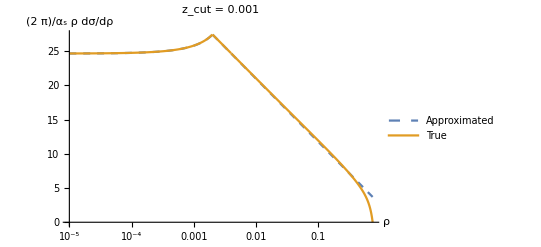

```mathematica
f[ρ_,z_]:=2HeavisideTheta[ρ-2z]Log[4/ρ]+2HeavisideTheta[2z-ρ]Log[1/(z-ρ/4)]-3/2

plot=LogLinearPlot[{2f[ρ,0.001],trueFull[ρ,0.001]},{ρ,0.00001,0.75},PlotLegends->{"Approximated", "True"},AxesLabel->{"ρ","(2  π)/α_s ρ dσ/dρ"},PlotStyle->{Dashed,Automatic},PlotLabel->"z_cut = 0.001"]
```

```mathematica
Export["plots/approximation_small_zcut.pdf",plot]
Export["plots/approximation_small_zcut.png",plot]
```

plots/approximation_small_zcut.pdf

plots/approximation_small_zcut.png